-Graphics-

# Statistical Distributions and Model Analysis

## Advanced Curve Fitting

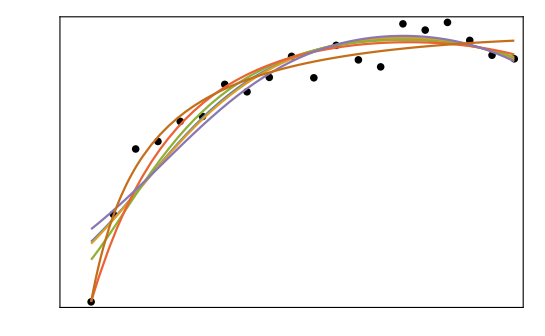

"Outline" |

### Webinar Part 1

Distribution Properties

Simulation of Distributions

Derived Distributions

Hypothesis Tests

Fitting Data to Distributions

Method of Moments Estimation

Bootstrapping & Confidence Estimation

### Webinar Part 2

Linear Model Fit

Nonlinear Model Fit

Fitting Theoretical Models

### Webinar Part 3

Generalized Linear Models

Piecewise Models

## Learning Objectives

The symbolic architecture of the Wolfram Language™ makes possible a uniquely convenient approach to working with statistical models. Starting from arbitrary data, the Wolfram Language generates symbolic representations of fitted models, from which a full spectrum of results and diagnostics can immediately be extracted, visualized or used in other computations.

### Generalized Linear Models

The Wolfram Language offers fitting of different types of regression models. This section uses real-world examples to explore some of these regression types:

Poisson regression

Logistic regression

Link functions

### Piecewise Models

Here, piecewise models are fitted using various approaches:

Piecewise NonlinearModelFit

Spline models

Automated curve fitting

## Generalized Linear Models

Generalized linear models belong to the family of regression models of the form ŷ==g^-1(β_0+β_1 x_1+β_2 x_2+…). The Wolfram Language has a built-in framework, GeneralizedLinearModelFit, for solving these types of problems.

In addition to the previously discussed two components: the independent terms (x_1, x_2, …), GeneralizedLinearModelFit allows specifying how the expected values of the response are related to a linear change in the independent variables via link function g.

Depending on the LinkFunction, the different models of regression can be created:

```mathematica
CellPrint[ExpressionCell[
table={{"Identity","Simple Linear Regresssion", "Gaussian"},{"Logit","Logistic Regresssion", "Binomial"},
{"Log","Poisson Regresssion", "Poisson"},
{"Reciprocal","Gamma Regresssion","Gamma "},{"Inverse Square","InverseGaussian Regression","InverseGaussian"}};
Grid[Prepend[table,{"Link","Regression Type","Link Function"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Left,Spacings->{4,2}],"Output",GeneratedCell->False]]
```

Link | Regression Type | Link Function
Identity | Simple Linear Regresssion | Gaussian
Logit | Logistic Regresssion | Binomial
Log | Poisson Regresssion | Poisson
Reciprocal | Gamma Regresssion | Gamma 
Inverse Square | InverseGaussian Regression | InverseGaussian

## Poisson Regression

The following data is the quarterly number of deaths from AIDS in Australia over the time period from January 1983 through June 1986:

```mathematica
aidsDat={0, 1, 2, 3, 1, 4, 9, 18, 23, 31, 20, 25, 37, 45};
```

The independent variables are just uniformly spaced time values, so take them to be 1-Length[aidsDat]. Fit two models, the first where just the count is taken and the second where the logarithm of the count is used. Since counts take integer values, you need to use ExponentialFamily → "Poisson":

```mathematica
mod1=GeneralizedLinearModelFit[aidsDat,{1,x},x,ExponentialFamily->"Poisson"]
```

```mathematica
mod2=GeneralizedLinearModelFit[aidsDat,{1,Log[x]},x,ExponentialFamily->"Poisson"]
```

Taking a look at the parameter tables shows that the estimates are more “significant” for the second model, even though the model is no more complex:

```mathematica
Row[{mod1["ParameterTable"],"   ",mod2["ParameterTable"]}]
```

Plots and AIC confirm that the model using logarithmic function fits much better. Both of these models are better in terms of reflecting the true nature of the data than a linear model fit (according to AIC):

```mathematica
mod3 = LinearModelFit[aidsDat, {1, x}, x]
```

```mathematica
Show[Plot[{mod3[t],mod1[t],mod2[t]},{t,1,14},PlotLegends->{Row[{"Linear AIC: ",mod3["AIC"]}],Row[{"GLM {1,x} AIC: ",mod1["AIC"]}],Row[{"GLM {1,Log[x]} AIC: ",mod2["AIC"]}]}],ListPlot[aidsDat,PlotMarkers-> Automatic]]
```

## Logistic Regression

The following dataset indicates the presence/absence of gold deposit as a function of water/chemical factors: As, Sb and presence/absence of lineament in the Hutti–Maski Schist Belt, Raichur, Karnataka, India [1]. The presence/absence of gold deposit is fitted in a logistic regression model to the arsenic and antimony levels and the lineament proximity to water.

### Data Import and Cleaning

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"gold_target1.dat"}]]
```

The last five rows are blank and the data is in string format. So just convert it to numbers and get rid of the last five rows:

```mathematica
golddat=ToExpression@data[[;;-5]];
```

### Fitting a Logistic Model

```mathematica
(mod1=GeneralizedLinearModelFit[golddat,{As,Sb,Ln},{As,Sb,Ln},ExponentialFamily->"Binomial"])//Normal
```

The logistic model is widely used and has a built-in function in the Wolfram Language, LogitModelFit. Equivalently, GeneralizedLinearModelFit with ExponentialFamily set to Binomial returns the same results:

```mathematica
mod2=(LogitModelFit[golddat,{As,Sb,Ln},{As,Sb,Ln}])//Normal
```

Computing the statistics (including BIC: Bayesian Information Criterion) and visualizing the residuals:

```mathematica
{mod1["ParameterTable"],ListPlot[mod1["FitResiduals"], Filling-> Axis,PlotRange-> All,PlotLegends->Row[{"BIC: ",mod1["BIC"],"   AIC: ",mod1["AIC"]}],ImageSize->400]}
```

[1] “Integration of Sparse Geologic Information in Gold Targeting Using Logistic Regression Analysis in the Hutti–Maski Schist Belt, Raichur, Karnataka, India—A Case Study,” Natural Resources Research, 8(3), 1999 pp. 233–250.

## Generalized Linear Models: Link Function

The canonical link functions and their corresponding type of regression have been discussed. Other link functions can be used for binomial data.

"Link" | "Formula"
Probit | √2 InverseErf[-1+2 y]
Cauchit | tan(π (x-1/2))
LogLog | -log(-log(y))
LogComplement | log(1-y)
ComplementaryLogLog | Log[-Log[1-y]]
OddsPowerLink | Piecewise[{{((y/(1-y))^α-1)/α, α≠0}, {log(y/(1-y)), α==0}}]
NegativeBinomialLink | log((α y)/(α y+1))

## Generalized Linear Model: "NegativeBinomialLink"

### Import and Clean Data

Here you can fit the number of terrorism incidences and their casualties in different provinces of Afghanistan, accumulated over 33 years, to various variables [2]. The variables include: opium production, population, area, mountainous, literacy, drinking water, nutrition, roads, infant mortality, Pashtun majority and foreign troops. Among these, the goal is to determine the most important influencing factors:

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"afghan_terror.dat"}]];
```

Look at how the data is interpreted in Mathematica:

```mathematica
data[[1]]//InputForm
```

### Fitting the Number of Incidents with "NegativeBinomialLink"

First, try to fit the number of incidents of terrorism occurring. Since the first entry is not one of the variables, you can eliminate it and then modify the data so that you can fit the number of incidents with the other variables:

```mathematica
dataincidents=data[[All,2;;]]/.{inc_,death_,opium_,pop_,area_,mountain_,literacy_,water_,food_,road_,infmortality_,Pashtun_,foreign_}-> {opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign,inc};
```

```mathematica
mod1=GeneralizedLinearModelFit[dataincidents,{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},ExponentialFamily->"Poisson",LinkFunction-> "NegativeBinomialLink"]
```

```mathematica
ListPlot[mod1["FitResiduals"], Filling-> Axis,PlotRange-> All,PlotLegends->Row[{"BIC: ",mod1["BIC"],"   AIC: ",mod1["AIC"]}]]
```

### Fitting the Number of Deaths

In this section, you can analyze the number of deaths. For that, modify the data accordingly:

```mathematica
datadeaths=data[[All,2;;]]/.{inc_,death_,opium_,pop_,area_,mountain_,literacy_,water_,food_,road_,infmortality_,Pashtun_,foreign_}-> {opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign,death};
```

Next, fit the data using all the variables:

```mathematica
(mod1=GeneralizedLinearModelFit[datadeaths,{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},ExponentialFamily->"Gaussian"])//Normal
```

```mathematica
{mod1["ParameterTable"],ListPlot[mod1["FitResiduals"],Filling-> Axis,PlotRange-> All,PlotLegends->Row[{"AICc: ",mod1["BIC"],"   AIC: ",mod1["AIC"]}],ImageSize->500]}
```

However, is this the best model? To find the best model fit, consider all subsets of the variables and find the model that corresponds to the largest of a statistical inference parameter—for example, AICc:

```mathematica
sub=Table[Join[{i},GeneralizedLinearModelFit[datadeaths,i,{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign},ExponentialFamily->"Gaussian"][{"AIC","BIC","LikelihoodRatioIndex","PearsonChiSquare"}]],{i,Subsets[{opium,pop,area,mountain,literacy,water,food,road,infmortality,Pashtun,foreign}]}];
```

Thus you can see that the most important variables are opium production, area, mountainous, water, roads and infant mortality:

```mathematica
Grid[Join[{{"Model","AICc","BIC","LikelihoodRatioIndex","PearsonChiSquare"}},Take[SortBy[sub,#[[2]]&],5]],Alignment->Left]
```

[2] J. A. Piazza, “The Opium Trade and Patterns of Terrorism in the Provinces of Afghanistan: An Empirical Analysis,” Terrorism and Political Violence, 24(2), 2012 pp. 213–234.

## Piecewise Continuous Model

### Import Data

The data in the set used here was collected by A. Filippelli at NIST.

Import some observational data from the NIST database:

```mathematica
filipDat= Sort[Import[FileNameJoin[{NotebookDirectory[],"Filipdata.txt"}],"Table"]];
```

Check the dimensions:

```mathematica
Dimensions[filipDat]
```

Visualize the data:

```mathematica
ListPlot[filipDat,GridLines-> Automatic]
```

It looks like fitting this data with three straight lines may be a good approach.

### Piecewise Continuous Model

Fit three lines to the data. Straight lines can be expressed in the form mx+b, and the intersection of two such lines can be given as a function of the two slopes and intercepts:

```mathematica
Clear[x,m1,m2,m3,b1,b2,b3]
```

Use Set and not SetDelayed here because you do not want to reconstruct the model every time it is used:

```mathematica
mdl[x,{m1,m2,m3,b1,b2,b3}]=With[{sol1= Solve[m1 x +b1==m2 x + b2,x],sol2= Solve[m2 x + b2==m3 x + b3,x]},
sols= Join[sol1,sol2];
{int1,int2}=x/.sols;
Piecewise[{{m1 x + b1, x<int1}, {m2 x + b2, int1≤ x<int2}, {m3 x + b3, int2≤ x}}]];
```

Use the model in NonlinearModelFit. Use constraints with the model and specify start values for the parameters estimated from the preceding plot:

```mathematica
pcwsMdl=NonlinearModelFit[filipDat,{mdl[x,{m1,m2,m3,b1,b2,b3}],-7.25<(-b1+b2)/(m1-m2)<-6.9,-6.1<(-b2+b3)/(m2-m3)<-4.9},{{m1,.1},{m2,1.0},{m3,.1},{b1,.75},b2,{b3,.87}},x]
```

The solution curve with the data points:

```mathematica
pcwsPlt=Plot[pcwsMdl[t],{t,-9,-3},Epilog-> {Red,Point[filipDat]},PlotLabel-> Style["Piecewise Model",18,Bold]]
```

The fit looks good, and you can get diagnostics from the fit.

A look at the residuals to see the goodness of fit:

```mathematica
ListPlot[pcwsMdl["FitResiduals"]]
```

## Smoothing Splines

The piecewise model used previously is not a linear model, as it is not expressed as a linear combination of basis vectors. By taking advantage of smoothing splines and using nonuniform knot spacings, you can generate linear b-splines (NURBS), using the Wolfram Language’s BSplineBasis function.

Visualize the data again and pay particular attention to the positions of the abrupt changes of direction in the data:

```mathematica
ListPlot[filipDat,GridLines-> Automatic]
```

The data goes approximately from -9 to -3, with sharp changes in direction around -7.2 and -6.1.

Generate the spline basis functions:

```mathematica
knts={-9,-7.2,-6.1,-3};
splns=Table[BSplineBasis[{1,knts},i,x],{i,0,1}]
```

Visualize the result:

```mathematica
Plot[splns,{x,-9,-3},GridLines-> Automatic]
```

Here is a function that will make things easier. It creates the basis for the fit and then applies LinearModelFit to the data and the basis set. You can use this as a model to create a function of your own to handle the sorts of cases you work with most often:

```mathematica
SplineModel[data_,knots_,dom:{x_,xmin_,xmax_},bs_List,deg_Integer]:=
Block[{basis,allKnots,n},
n=Length[knots]+2;
basis=bs~Join~Table[BSplineBasis[{deg,Join[{xmin},knots,{xmax}]},i,x],{i,0,n-3}];
LinearModelFit[data,basis,x]
]
```

Fit the data:

```mathematica
smoothFit=SplineModel[filipDat,{-7.2,-6.1},{x,-9,-3},x^Range[0,1],1]
```

This shows plots of the two different fits:

```mathematica
GraphicsRow[{pcwsPlt,Plot[smoothFit[t],{t,-9,-3},Epilog-> {Red,Point[filipDat]},PlotLabel-> Style["Spline Smoothing Model",18,Bold]]},ImageSize-> 10 72]
```

A table of results:

```mathematica
Grid[{{Style["piecewise model","Subsection"],Style["spline smoothing model","Subsection"]},{Style[StringForm["Adjusted R squared `1`",NumberForm[pcwsMdl["AdjustedRSquared"],{5,6}]],"Text"],Style[StringForm["Adjusted R squared `1`",NumberForm[smoothFit["AdjustedRSquared"],{5,6}]],"Text"]},{ListPlot[pcwsMdl["FitResiduals"],PlotLabel-> Style["fit residuals","Text"],ImageSize-> Medium],ListPlot[smoothFit["FitResiduals"],PlotLabel-> Style["fit residuals","Text"],ImageSize-> Medium]}},Frame-> All]
```

```mathematica
Clear[smoothFit,pcwsMdl,filipDat]
```

## Automated Curve Fitting

FindFormula can be used for automated curve fitting, with no prior knowledge of the underlying function.

In this example, you can perform an automated fitting to the GDP of the United States for the last half century or so.

First, obtain the data from the Entity framework, then convert the time series to a list of unitless values:

```mathematica
(*GDP=Normal@EntityValue[Entity["Country","UnitedStates"],EntityProperty["Country","GDP",{"Date"-> Interval[{DateObject[{1960},"Year","Gregorian",-5.],DateObject[{2015},"Year","Gregorian",-5.]}]}]];*)
```

```mathematica
GDPnounits=Table[{i+1959,QuantityMagnitude@GDP[[i,2]]},{i,1,Length[GDP]}];
```

Find the best 5 fits to the data and evaluate the loss, score (AICc) and the complexity of the models:

```mathematica
FindFormula[GDPnounits,x,5,All, PerformanceGoal->"Quality"]
```

Visualize the best fit:

```mathematica
fits = FindFormula[GDPnounits, x,PerformanceGoal->"Quality"];
```

```mathematica
Show[ListPlot[GDPnounits,PlotStyle->Directive[Red,PointSize[Medium]]], Plot[fits, {x, 1955, 2020}, PlotRange->All,PlotStyle->Black]]
```

## Glossary

AbsoluteTime | Array | Automatic | BIC | Binomial
Block | Bold | BSplineBasis | DateListPlot | DateObject
Dimensions | Directive | Entity | EntityProperty | EntityValue
Epilog | ExponentialFamily | FileNameJoin | Filling | FinancialData
FindFormula | FitResiduals | Gaussian | GeneralizedLinearModelFit | GraphicsRow
Grid | GridLines | ImageSize | Import | Interval
Join | Length | LikelihoodRatioIndex | LinearModelFit | LinkFunction
ListPlot | Log | LogitModelFit | NegativeBinomialLink | None
Normal | NotebookDirectory | NumberForm | ParameterTable | PearsonChiSquare
PerformanceGoal | Plot | PlotLabel | PlotLegends | PlotMarkers
PlotRange | PlotStyle | Point | Poisson | Quality
QuantityMagnitude | Red | Row | Show | Solve
Sort | SortBy | StringForm | Style | Subsets
Table | Take | Ticks | TimeSeries | ToExpression
With |  |  |  |

## Review Exercises

#### Provided Separately

## Initialize Cells

```mathematica
GDP={{DateObject[{1960,1,1},"Day","Gregorian",-5.],Quantity[5.433*^11, US dollars per year]},{DateObject[{1961,1,1},"Day","Gregorian",-5.],Quantity[5.633*^11, US dollars per year]},{DateObject[{1962,1,1},"Day","Gregorian",-5.],Quantity[6.051*^11, US dollars per year]},{DateObject[{1963,1,1},"Day","Gregorian",-5.],Quantity[6.386*^11, US dollars per year]},{DateObject[{1964,1,1},"Day","Gregorian",-5.],Quantity[6.858*^11, US dollars per year]},{DateObject[{1965,1,1},"Day","Gregorian",-5.],Quantity[7.437*^11, US dollars per year]},{DateObject[{1966,1,1},"Day","Gregorian",-5.],Quantity[8.15*^11, US dollars per year]},{DateObject[{1967,1,1},"Day","Gregorian",-5.],Quantity[8.617*^11, US dollars per year]},{DateObject[{1968,1,1},"Day","Gregorian",-5.],Quantity[9.425*^11, US dollars per year]},{DateObject[{1969,1,1},"Day","Gregorian",-5.],Quantity[1.0199*^12, US dollars per year]},{DateObject[{1970,1,1},"Day","Gregorian",-5.],Quantity[1.075884*^12, US dollars per year]},{DateObject[{1971,1,1},"Day","Gregorian",-5.],Quantity[1.16777*^12, US dollars per year]},{DateObject[{1972,1,1},"Day","Gregorian",-5.],Quantity[1.282449*^12, US dollars per year]},{DateObject[{1973,1,1},"Day","Gregorian",-5.],Quantity[1.428549*^12, US dollars per year]},{DateObject[{1974,1,1},"Day","Gregorian",-5.],Quantity[1.548825*^12, US dollars per year]},{DateObject[{1975,1,1},"Day","Gregorian",-5.],Quantity[1.688923*^12, US dollars per year]},{DateObject[{1976,1,1},"Day","Gregorian",-5.],Quantity[1.877587*^12, US dollars per year]},{DateObject[{1977,1,1},"Day","Gregorian",-5.],Quantity[2.085951*^12, US dollars per year]},{DateObject[{1978,1,1},"Day","Gregorian",-5.],Quantity[2.356571*^12, US dollars per year]},{DateObject[{1979,1,1},"Day","Gregorian",-5.],Quantity[2.632143*^12, US dollars per year]},{DateObject[{1980,1,1},"Day","Gregorian",-5.],Quantity[2.862505*^12, US dollars per year]},{DateObject[{1981,1,1},"Day","Gregorian",-5.],Quantity[3.210956*^12, US dollars per year]},{DateObject[{1982,1,1},"Day","Gregorian",-5.],Quantity[3.344991*^12, US dollars per year]},{DateObject[{1983,1,1},"Day","Gregorian",-5.],Quantity[3.638137*^12, US dollars per year]},{DateObject[{1984,1,1},"Day","Gregorian",-5.],Quantity[4.040693*^12, US dollars per year]},{DateObject[{1985,1,1},"Day","Gregorian",-5.],Quantity[4.346734*^12, US dollars per year]},{DateObject[{1986,1,1},"Day","Gregorian",-5.],Quantity[4.590155*^12, US dollars per year]},{DateObject[{1987,1,1},"Day","Gregorian",-5.],Quantity[4.870217*^12, US dollars per year]},{DateObject[{1988,1,1},"Day","Gregorian",-5.],Quantity[5.252629*^12, US dollars per year]},{DateObject[{1989,1,1},"Day","Gregorian",-5.],Quantity[5.657693*^12, US dollars per year]},{DateObject[{1990,1,1},"Day","Gregorian",-5.],Quantity[5.979589*^12, US dollars per year]},{DateObject[{1991,1,1},"Day","Gregorian",-5.],Quantity[6.174043*^12, US dollars per year]},{DateObject[{1992,1,1},"Day","Gregorian",-5.],Quantity[6.539299*^12, US dollars per year]},{DateObject[{1993,1,1},"Day","Gregorian",-5.],Quantity[6.878718*^12, US dollars per year]},{DateObject[{1994,1,1},"Day","Gregorian",-5.],Quantity[7.308755*^12, US dollars per year]},{DateObject[{1995,1,1},"Day","Gregorian",-5.],Quantity[7.66406*^12, US dollars per year]},{DateObject[{1996,1,1},"Day","Gregorian",-5.],Quantity[8.100201*^12, US dollars per year]},{DateObject[{1997,1,1},"Day","Gregorian",-5.],Quantity[8.608515*^12, US dollars per year]},{DateObject[{1998,1,1},"Day","Gregorian",-5.],Quantity[9.089168*^12, US dollars per year]},{DateObject[{1999,1,1},"Day","Gregorian",-5.],Quantity[9.660624*^12, US dollars per year]},{DateObject[{2000,1,1},"Day","Gregorian",-5.],Quantity[1.0284779*^13, US dollars per year]},{DateObject[{2001,1,1},"Day","Gregorian",-5.],Quantity[1.0621824*^13, US dollars per year]},{DateObject[{2002,1,1},"Day","Gregorian",-5.],Quantity[1.0977514*^13, US dollars per year]},{DateObject[{2003,1,1},"Day","Gregorian",-5.],Quantity[1.151067*^13, US dollars per year]},{DateObject[{2004,1,1},"Day","Gregorian",-5.],Quantity[1.2274928*^13, US dollars per year]},{DateObject[{2005,1,1},"Day","Gregorian",-5.],Quantity[1.3093726*^13, US dollars per year]},{DateObject[{2006,1,1},"Day","Gregorian",-5.],Quantity[1.3855888*^13, US dollars per year]},{DateObject[{2007,1,1},"Day","Gregorian",-5.],Quantity[1.4477635*^13, US dollars per year]},{DateObject[{2008,1,1},"Day","Gregorian",-5.],Quantity[1.4718582*^13, US dollars per year]},{DateObject[{2009,1,1},"Day","Gregorian",-5.],Quantity[1.4418739*^13, US dollars per year]},{DateObject[{2010,1,1},"Day","Gregorian",-5.],Quantity[1.4964372*^13, US dollars per year]},{DateObject[{2011,1,1},"Day","Gregorian",-5.],Quantity[1.5517926*^13, US dollars per year]},{DateObject[{2012,1,1},"Day","Gregorian",-5.],Quantity[1.6155255*^13, US dollars per year]},{DateObject[{2013,1,1},"Day","Gregorian",-5.],Quantity[1.6691517*^13, US dollars per year]},{DateObject[{2014,1,1},"Day","Gregorian",-5.],Quantity[1.7393103*^13, US dollars per year]},{DateObject[{2015,1,1},"Day","Gregorian",-5.],Quantity[1.8036648*^13, US dollars per year]}};
```